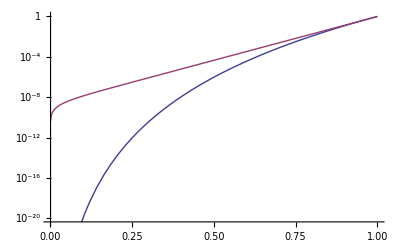

```mathematica
LogPlot[{x^20,(Exp[20x]-1)/Exp[20]},{x,0.001,1}]
```

```mathematica
Erad[x_,y_,x0_,y0_]:=1/((x-x0)^2+(y-y0)^2)
```

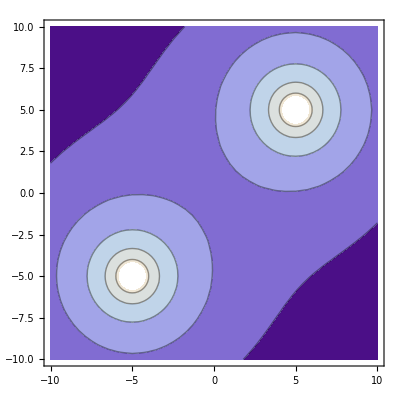

```mathematica
ContourPlot[Log[Erad[x,y,-5,-5]+Erad[x,y,5,5]],{x,-10,10},{y,-10,10}]
```